## Multi-View Reconstruction (Image + Geometry + Optical Flow)

A 3D object can be reconstructed from multiple 2D views. ImageDisplacements is used to determine the parallax from one view to the next. The larger the parallax shift, the closer the object behind the corresponding pixel. With this depth information, you can extrude the vertices of an object mesh obtained through ImageMesh and TriangulateMesh. The result is displayed via texture mapping on the 3D mesh object.

```mathematica
imgs={-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
<<NateCam`
```

```mathematica
(* r= currentImage[]*)
```

```mathematica
(*c=  currentImage[]*)
```

```mathematica
(*l = currentImage[]*)
```

```mathematica
saved = {-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
makeMask[im_]:=Erosion[Binarize[Blur[Binarize[ImageSubtract[ColorSeparate[im][[{1,2}]]], 0],4], 0],0]
stripBack[im_]:=ImageMultiply[makeMask[im], im]
```

```mathematica
imgs = stripBack/@Function[im, ImageCrop[im, {240,240}, Center]]/@saved;Function[x,HighlightImage[x,makeMask[x]]]/@imgs
```

{-Graphics-,-Graphics-,-Graphics-}

Obtain an object mask of the central image.

```mathematica
mask=Erosion[Binarize[imgs⟦2⟧,0],1]
```

-Graphics-

Determine the parallax in the left and right images with respect to the center image.

```mathematica
parallaxL=First@ImageDisplacements[imgs⟦{2,1}⟧];
```

```mathematica
parallaxR=First@ImageDisplacements[imgs⟦{2,3}⟧];
```

Combine these displacements in a total parallax.

```mathematica
parallax=parallaxL-parallaxR;
```

In the given setting, the x component of the parallax is roughly proportional to the depth of the respective pixel source.

```mathematica
depth = Blur@Opening[ImageMultiply[ImageAdjust@Image[parallax⟦All,All,1⟧],mask],DiskMatrix[4]]
```

-Graphics-

Construct a depth function.

```mathematica
depthFunction = ListInterpolation[Transpose@Reverse@ImageData[depth]];
```

Obtain an object mesh with a refinement that depends on the object's saliency.

```mathematica
resolution=ImageAdjust@ImageSaliencyFilter[imgs⟦2⟧];
```

```mathematica
resolutionFunction = ListInterpolation[Transpose@Reverse@ImageData@resolution];
```

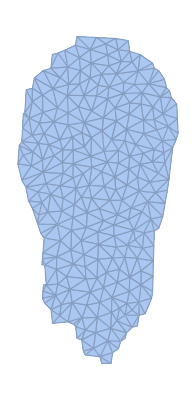

```mathematica
Ω=TriangulateMesh[
ImageMesh[Erosion[mask,DiskMatrix[2]]],MeshRefinementFunction->Function[{vertices,area},area>32+512(1-resolutionFunction@@Mean[vertices])^6]
]
```

Extrude the object mesh with the depth function.

```mathematica
Graphics3D[
GraphicsComplex[
Apply[{##,depthFunction[##]}&,MeshCoordinates[Ω],{1}],
{EdgeForm[],MeshCells[Ω,2]}
],
PlotRange-> Append[Thread[{0,ImageDimensions[mask]}],{0,1}],
BoxRatios-> {1,1,2/3},
ViewPoint->Top
]
```

-Graphics3D-

Extract the object texture from the central image.

```mathematica
texture = SetAlphaChannel[imgs⟦2⟧,mask]
```

-Graphics-

Map the texture onto the 3D object.

```mathematica
Graphics3D[
{Texture[texture],
GraphicsComplex[
Apply[{##,depthFunction[##]}&,MeshCoordinates[Ω],{1}],
{EdgeForm[],MeshCells[Ω,2]},
VertexTextureCoordinates-> Map[#/ImageDimensions[texture]&,MeshCoordinates[Ω]]
]
},
PlotRange-> Append[Thread[{0,ImageDimensions[mask]}],{0,1}],
BoxRatios-> {1,1,2/3},
Lighting-> {{"Ambient",White}},
ViewPoint-> Top,
Boxed->False
]
```

-Graphics3D-